```mathematica
(*
This notebook takes in external fields from file, inputs them  into the geometry of the 1 D system and calcualtes the majorana wavefunctions and energy levels. One can control the superconducting gap to alter the energy needed through the zemman coupling provided by the magnetic field, one can also change the gates (energy offsets) to change couplings
The geomtry here is a single wire.*)
```

```mathematica
(*also can change^2 couplings energy gates offsets one the to*)
```

```mathematica
Clear[fileXTop, fileYTop, fileXLeg, fileYLeg];
(*ClearAll;*)

If[runCounter==0,
runCounter=1]
runCounter=runCounter+1
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+runCounter.

Hold[If[runCounter==0,runCounter=1]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+runCounter.

Hold[runCounter=runCounter+1]

```mathematica
(*MuMax: no hysteresis - Two Wires - standard gap*)
TwoWireMMTNoHystCondition =0;
If[TwoWireMMTNoHystCondition==1,
inputfile=ImportString["/Users/malcolmjardine/Box\ Sync/MacBook\ Files/Documents/Pittburgh\ Uni/Research/Professor\ Sergey\ Frolov/Majorana\ Fermions/The_Malcolm_Project-master/C_Braiding/Magnetic_Field_Profiles/TwoWire/StandardGap_1000/table.txt"];
FieldData=Import[inputfile,"Table"];
(*FilePrint[inputfile]*)(*Prints out data*)

lengthOfData=Length[FieldData[[All,1]]];(*Gives the length of the column (or number of rows*)
TopRowStart=2+0;
TopRowEnd = 284-0;
BxColumStart = 17;

MagXTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart]];
MagYTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+1]] ;
(*MagYLeg=FieldData[[TopRowStart;;TopRowEnd,BxColumStart]];
MagXLeg=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+1]] ;*)(*As By is next collum over*)
(*BxData=heatMapData[[lengthOfBxData+1;;ByRowEnd,BxColumStart+1]]*)
topNumPoints = Length[MagXTop];
fileInfo="TwoWire_NoHysteresis_Standard";
]
```

```mathematica
(*MuMax:no hysteresis closer*)TwoWireNoHysteresisMiddleMag222=0;
If[TwoWireNoHysteresisMiddleMag222==1,inputfile=ImportString["C:\\Program Files\\mumax3.9.1_windows\\RunFiles\\TwoWire_NoHysteresis_MiddleMag_222.out\\table.txt"];
FieldData=Import[inputfile,"Table"];
(*FilePrint[inputfile]*)(*Prints out data*)lengthOfData=Length[FieldData[[All,1]]];(*Gives the length of the column (or number of rows*)
cutedges=0;
TopRowStart=2+cutedges;
TopRowEnd=lengthOfData-cutedges;
BxColumStart=17;
MagXTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart]];
MagYTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+1]];
MagZTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+2]];
(*MagYLeg=FieldData[[TopRowStart;;TopRowEnd,BxColumStart]];
MagXLeg=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+1]];*)(*As By is next collum over*)(*BxData=heatMapData[[lengthOfBxData+1;;ByRowEnd,BxColumStart+1]]*)topNumPoints=Length[MagXTop];
fileInfo="TwoWire_NoHysteresis_MiddleMag_222";
]
(*topNumPoints=Length[MagXTop]*)
```

```mathematica
(*MuMax:no hysteresis closer*)TJuncNoHysteresis222=1;
If[TJuncNoHysteresis222==1,inputfile=ImportString["C:\\Program Files\\mumax3.9.1_windows\\RunFiles\\Tjunc_NoHysteresis_Firework_222.out\\table.txt"];
FieldData=Import[inputfile,"Table"];
(*FilePrint[inputfile]*)(*Prints out data*)
lengthOfData=Length[FieldData[[All,1]]]; (*Gives the length of the column (or number of rows*)

pointsTOPWire=FieldData[[2,25]]+1; (*Number of data points of top wire*)

cutedges=0; (*Cutting of points of  Top data*)
TopRowStart=2+cutedges;
TopRowEnd=pointsTOPWire-cutedges;
BxColumStart=17;

LegRowStart =pointsTOPWire + 1;

MagXTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart]];
MagYTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+1]];
MagZTop=FieldData[[TopRowStart;;TopRowEnd,BxColumStart+2]];

MagXLeg=FieldData[[LegRowStart;;lengthOfData,BxColumStart+3]];
MagYLeg=FieldData[[LegRowStart;;lengthOfData,BxColumStart+4]]; (*As By is next collum over*)

topNumPoints=Length[MagXTop];
legNumPoints=Length[MagYLeg];
fileInfo="TJunc_NoHysteresis_222";]
(*topNumPoints=Length[MagXTop]*)
```

```mathematica
(*Fixing a single NaN value, replacing with mean of two neignouring points *)
NaNPosition=First[First[Position[MagXTop,"NaN"]]];
MeanVal =Mean[Table[MagXTop[[ppp]],{ppp,{NaNPosition-1,NaNPosition+1}}] ];
MagXTop = MagXTop/.{"NaN"->MeanVal};

NaNPositionY=First[First[Position[MagYTop,"NaN"]]];
MeanVal =Mean[Table[MagYTop[[ppp]],{ppp,{NaNPositionY-1,NaNPositionY+1}}] ];
MagYTop = MagYTop/.{"NaN"->MeanVal};

(*NaNPosition=First[First[Position[MagXLeg,"NaN"]]];
MeanVal =Mean[Table[MagXLeg[[ppp]],{ppp,{NaNPosition-1,NaNPosition+1}}] ];
MagXLeg= MagXLeg/.{"NaN"->MeanVal};

NaNPositionY=First[First[Position[MagYLeg,"NaN"]]];
MeanVal =Mean[Table[MagYLeg[[ppp]],{ppp,{NaNPositionY-1,NaNPositionY+1}}] ];
MagYLeg = MagYLeg/.{"NaN"->MeanVal};*)
```

First::nofirst: {} has zero length and no first element.

```mathematica
(*MiddleNumPointsField=90;
(*MiddleNumPointsField=100;*)(*10 is 100nm if total number of sites is 2000nm*)
LeftRightNumPointsField=(86-MiddleNumPointsField/2);

(*Origional step field*)
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];

MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];
topNumPoints=Length[MagXTop];
fileInfo="TwoWireMMT_NoHysteresis_FakeField";*)

(*Double swtich with gap in middle *)
(*MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField}],Table[0,{n,1,20}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,20}],Table[0,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[xfield,{n,1,20}],Table[0,{n,1,MiddleNumPointsField}],Table[FlipFirstHalf*xfield,{n,1,20}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];*)

(*4 swtiches of Bx with By in gaps*)
(*MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];

MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];*)

(*Linear Ramp*)
(*linearRamp=Table[2*xfield/MiddleNumPointsField*n-xfield,{n,1,MiddleNumPointsField}];
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],linearRamp,Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];*)

(*Similar to two wire field*)
(*spaceBetween=10;
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];
yfieldSmallSpace=10;
yfieldSmall=-0.07;
(*yfieldSmall=0;*)MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],Table[0,{n,1,1}]];
topNumPoints=Length[MagXTop];*)
(*Similar to two wire field*)
```

-0.14

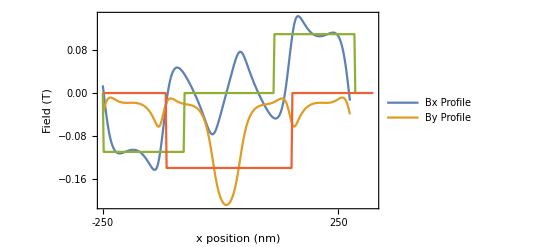

```mathematica
(*-------------------------------------------------------------------------------------*)(*-------------------------------------------------------------------------------------*)(*-------------------------------------------------------------------------------------*)

(*Total Field points is 200, this represents the whole wire*)
MiddleNumPointsField=100;
(*MiddleNumPointsField=100;*) (*10 is 100nm if total number of sites is 2000nm*)
LeftRightNumPointsField =(140-MiddleNumPointsField/2);
xfield=0.11;
(*yfield=0*)
yfield=-0.14



FlipFirstHalf=-1;


(*Similar to two wire field*)
spaceBetween=-0;
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];
yfieldSmallSpace=0;
yfieldSmall=-0.0;
(*yfieldSmall=0;*)MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],Table[0,{n,1,1}]];
topNumPoints=Length[MagXTop];
(*Similar to two wire field*)

yfieldSmallSpace2=20;
MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace2}],Table[yfield,{n,1,MiddleNumPointsField+2*yfieldSmallSpace2}],Table[0,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];


(*Similar to two wire field-chain*)
(*spaceBetween=20;
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],
Table[0,{n,1,1}]];
yfieldSmallSpace=10;
yfieldSmall=-0.0;
(*yfieldSmall=0;*)
MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,LeftRightNumPointsField-2*yfieldSmallSpace}],Table[-yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[-yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[-yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,MiddleNumPointsField-2*spaceBetween}],
Table[0,{n,1,1}]];
topNumPoints=Length[MagXTop];*)
(*Similar to two wire field - chain*)

(*Similar to two wire field-chain*)
(*spaceBetween=20;
MagXTop3=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,1}]];
yfieldSmallSpace=10;
yfieldSmall=-0.0;
(*yfieldSmall=0;*)
MagYTop3=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,LeftRightNumPointsField-2*yfieldSmallSpace}],Table[-yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[-yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[-yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,LeftRightNumPointsField-2*yfieldSmallSpace}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,spaceBetween}],Table[yfield,{n,1,MiddleNumPointsField-2*spaceBetween}],Table[0,{n,1,spaceBetween}],Table[yfieldSmall,{n,1,yfieldSmallSpace}],Table[0,{n,1,LeftRightNumPointsField-yfieldSmallSpace}],
Table[0,{n,1,1}]];
topNumPoints=Length[MagXTop];*)
(*Similar to two wire field-chain*)


(*MagXTop = MagXTop3;
MagYTop = MagYTop3;*)
fileInfo="TwoWireMMT_NoHysteresis_FakeField";



(*Flippinng second half of Field *)
(*MagXTop=Join[MagXTop[[1;;(Round[Length[MagXTop]/2]) ]],Reverse[MagXTop[[1;;(Round[Length[MagXTop]/2])]]]
];*)

(*Reapeating field profile Field*)
(*MagXTop3=Join[MagXTop,Reverse[MagXTop[[71;;203]]],MagXTop(*,Reverse[MagXTop[[71;;203]]],MagXTop*)];
MagYTop3=Join[MagYTop,Reverse[-MagYTop[[71;;203]]],MagYTop(*,Reverse[MagYTop[[71;;203]]],MagYTop*)];
topNumPoints = Length[MagXTop];
legNumPoints = Length[MagXTop];*)

(*MagXTop=Join[Table[0,{n,1,1}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],

Table[0,{n,1,MiddleNumPointsField}],Table[FlipFirstHalf*xfield,{n,1,LeftRightNumPointsField}],Table[0,{n,1,MiddleNumPointsField}],Table[xfield,{n,1,LeftRightNumPointsField}],
Table[0,{n,1,1}]];

MagYTop=Join[Table[0,{n,1,1}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],

Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,LeftRightNumPointsField}],
Table[0,{n,1,1}]];
topNumPoints = Length[MagXTop];
legNumPoints = Length[MagXTop];*)
(*MagYTop=Table[0,{ddd,1,topNumPoints}];*)

topNumPoints=Length[MagXTop];
(*Having certain number of ticks and then putting what I want in certain postions*)
lst1=Table[{i,""},{i,1,topNumPoints,topNumPoints/20}];
lst2 = lst1/.{List[1,""]->{1,"-250"},List[First[Last[lst1]],""]->{First[Last[lst1]],"250"}};
ListPlot[{MagXTop,MagYTop,MagXTop3,MagYTop3},PlotRange->All,Joined->True,InterpolationOrder->1,
PlotLegends->{"Bx Profile","By Profile"},
PlotLabel->None,LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]},ImageSize->400,Frame->True,FrameLabel->{{HoldForm["Field (T)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{lst2,lst1}},PlotRangePadding->0.01]
```

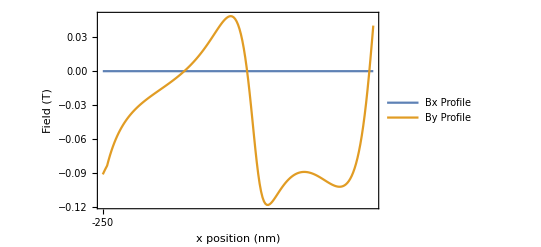

```mathematica
(*MagXTop={0,0};
MagYTop={0,0};*)

yfield2=0.14;
(*yfield2=0;*)

(*MagXLeg=Join[Table[0,{n,1,MiddleNumPointsField}]];
MagYLeg=Join[Table[yfield*0.7,{n,1,20}],Table[0,{n,1,LeftRightNumPointsField}],Table[yfield,{n,1,MiddleNumPointsField}],Table[0,{n,1,1}]];*)
(*MagYLeg=Join[Table[-yfield2,{n,1,MiddleNumPointsField}],Table[0,{n,1,1}]];
MagXLeg=Table[-0.07,{n,1,Length[MagYLeg]}];*)

legNumPoints = Length[MagYLeg];
lst1=Table[{i,""},{i,1,topNumPoints,topNumPoints/20}];
lst2 = lst1/.{List[1,""]->{1,"-250"},List[First[Last[lst1]],""]->{First[Last[lst1]],"250"}};
ListPlot[{MagXLeg,MagYLeg},PlotRange->All,Joined->True,InterpolationOrder->1,
PlotLegends->{"Bx Profile","By Profile"},
PlotLabel->None,LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]},ImageSize->400,Frame->True,FrameLabel->{{HoldForm["Field (T)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{lst2,lst1}},PlotRangePadding->0.01]
```

```mathematica
(*tst=Import[fileXTop,{"Lines",1}];*)
SetDirectory[NotebookDirectory[]]; 
(*Setting where plots are created to current folder where this file is (or telling path to start from here)*)
CreateDirectory[StringJoin[{"Mathematica_out/",fileInfo,"/"}]];
```

CreateDirectory::filex: C:\Users\Frolov Labuser\Documents\MalcolmJ\Mathematica\Majorana Code\Mathematica_out\TwoWireMMT_NoHysteresis_FakeField\ already exists.

```mathematica
magBTop=1000*Table[
Sqrt[(MagXTop[[ppp]])^2+(MagYTop[[ppp]])^2],{ppp,1,Length[MagYTop]}
];
```

```mathematica
anglesBTop=Table[
ArcTan[MagXTop[[ppp]],MagYTop[[ppp]]]/Degree//FullSimplify,{ppp,1,Length[MagYTop]}
];
180+anglesBTop;
```

```mathematica
ImageResize[ResourceFunction["CombinePlots"][
postionx1=0.5;
postiony1=0.2;
ListPlot[magBTop,Joined->True,InterpolationOrder->1,PlotRange->{Automatic,{0,Max[magBTop]}},LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]},ImageSize->{400},AspectRatio->1/4,PlotStyle->{Blue,Thickness[0.006]},FrameLabel->{{HoldForm[(*"Magnitude of Field (mT)"*)"|B| (mT)"],None},{HoldForm["x position (nm)"],None}},
Frame->True,FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{lst2,lst1}},PlotRangePadding->None

(*,PlotLegends->Placed[{"Bx Profile","By Profile"},{postionx1,postiony1}]*)],

ListPlot[(180+anglesBTop),Joined->True,InterpolationOrder->1, Frame->True,LabelStyle->{FontFamily->"Helvetica",18,GrayLevel[0],Red},(*PlotLegends->Placed[{"By Profile"},{postionx1,postiony1}],*)PlotStyle->{Red,Thickness[0.006]},FrameLabel->(*"Angle from negative x-axis"*)"θ from negative x-axis",FrameStyle->Black,
FrameTicksStyle->{Red,Red,Red,Red},PlotStyle->{Blue,Directive[Red,Dashed]},PlotRange->{Automatic,{0,200}},FrameTicks->{{{0,30,60,90,120,150,180},Automatic},{lst2,lst1}}],

"AxesSides"->"TwoY"],{All,All}]
```

-Graphics-

```mathematica
(*ImageResize[ListLinePlot[magBTop,ColorFunction->Function[{x,y},Hue[x]],Filling->Axis,Frame->True,FillingStyle->Automatic,ImageSize->{500,500}],{All,200}];*)
```

```mathematica
(*
Plot[Sin[x],{x,0,2 Pi},ColorFunction->Function[{x,y},Hue[x]],Filling->Axis,FillingStyle->Automatic];
*)
```

```mathematica
(*ListLinePlot[magBTop,Filling->Axis,FillingStyle->Automatic,ColorFunction->{0.1}];

Plot[Abs[Exp[2 I x-x^2/2]],{x,-4,4},Filling->Axis,FillingStyle->Automatic,ColorFunction->Function[{x,y},Hue[Rescale[Arg[Exp[2 I x-x^2/2]],{-4,4}]]],ColorFunctionScaling->False];
rescaleList = Rescale[testlist,{Min[testlist],Max[testlist]},{0,1}];
magBTop;
Rescale[magBTop,{-3,3}];
*)
```

```mathematica
(*ListLinePlot[testlist = {-1,-0.5,0,0.5,1},Filling->Axis,FillingStyle->Automatic,
ColorFunction->Hue[Rescale[testlist,{Min[testlist],Max[testlist]},{0,1}]],ColorFunctionScaling->False];
Rescale[testlist,{Min[testlist],Max[testlist]},{0,1}];*)
```

```mathematica
(**)
```

```mathematica
(*testlist = {5,5,2,2,-10,-10,-1,-0.5,0,0,0.5,0.5,1,1,5};
ListLinePlot[testlist,
ColorFunction->Function[{x,y},Hue[{y}]],Filling->Axis,ColorFunctionScaling->True];*)
```

```mathematica
(*
ListLinePlot[Sinc[Range[0,10,0.1]],ColorFunction->Function[{x,y},Hue[x]],Filling->Axis];*)
```

```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31);   (*Electron mass in Kg*)
e0=1.602176487*10^(-19); (*Electron charge in C*)
ηm=hbar^2*e0*10^(20)/m0 ; (* hbar^2/m0 in eV A^2 *)
μB=1000*5.7883818066 * 10^(-5);    (* in meV/T *)
(*meVpK=8.6173325*10^(-2); *)  (* Kelvin into meV *)
(* **************************************** *)
Clear[ts, as, ms, Nx, NxM,Nx3, α0, α, SOCLength, Δ,geff];
geff=50; (*Lande factor for nanowire*)
as=10.0; (* unit cell in A *)
ms=0.04;(* effetcive mass*)
ts=1000*ηm/(2*as^2*ms); (* hopping in meV - origional: 500*ηm/(2*as^2*ms); *)
α0=0.203; (*0.203 Rahsba coupling constant - eV.A*)
α=1000*α0/as; (* Rashba coupling in meV *)
Δ=0.09; (* induced gap in meV *)
SOCLength =  10^(9)*hbar^2*e0/(ms*m0*(α0* 10^(-10)))(*Spin orbit length, for reference - nm*)


NxM=200;(*Number of points for middle section  *)
Nx=(*2800+*)2*2150/2-NxM/2 (*Number of points for each top wire sections *)(*Keeping total number of points at a certain amount so length of system is the same when changing middle section*)
Nx3=2*(1075+300);(*Number of points or leg wire*)

(*Nxn=0;*)
(*Ny=1;*)
totalNumPlotPointsX = 2*Nx+NxM; (*Number of points data is strecthed in Top to for Majorana use*)
totalNumPlotPointsY = Nx3; (*Number of points data is strecthed in leg to for Majorana use*)
(*asw=600.0/(Ny+1);*)
(*αw=α*as/asw;*)
(*tsw=4.0;*)

μ=0;
(*μ=2ts Cos[Pi/(Nx+1.0)]-2ts Cos[Pi/(2*Nx+NxM+1.0)];*) (*Use this when adjusting middle section size*)

legOnOff=1;

tϕ1=1*ts;
tϕ2=1*ts;
tϕ3=1*legOnOff*ts;

SOCMiddle=1;
GapMiddle=1;


yFieldSwitch=1;

ϕ=0(*0.5 π*); (*Phase difference of top two wire superconducotrs?*)
ϕ3=0;(*Phase difference of bottom superconducotr?*)
gx=0.5*μB*geff; (*Zeeman energy term in meV/T*)
gy=yFieldSwitch*0.5*μB*geff;
(*No addition*)
ex = 0.0;
ey = 0.0;
```

93.8419

2050

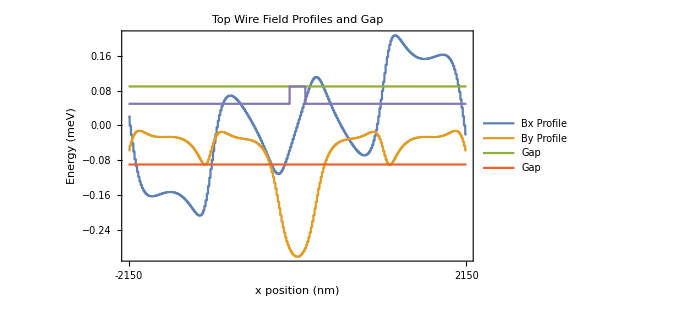

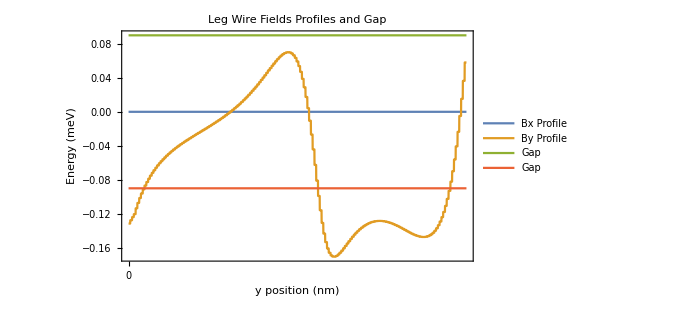

```mathematica
MagΔXTop=Table[ex+gx*MagXTop[[Ceiling[ii*Length[MagXTop]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
MagΔYTop=Table[ey+gy*MagYTop[[Ceiling[ii*Length[MagYTop]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
GapTop=Table[Δ,{i,1,Length[MagΔXTop]}];
MagΔXLeg=Table[ex+gx*MagXLeg[[Ceiling[ii*Length[MagXLeg]/(Nx3)]]],{ii,1,Nx3}];
MagΔYLeg=Table[ey+gx*MagYLeg[[Ceiling[ii*Length[MagYLeg]/(Nx3)]]],{ii,1,Nx3}];
GapLeg=Table[Δ,{i,1,Length[MagΔXLeg]}];

HeightMiddleSection = Max[Abs[GapTop]];
MiddleSection=Join[Table[0.05,{lll,1,Nx}],Table[HeightMiddleSection,{lll,1,NxM}],Table[0.05,{lll,1,Nx}]];

(*Picking where and what I want the ticks to say for plot*) 
(*Angled mags Long wire*)
emptyTickPosXTop=Table[{i,""},{i,1,totalNumPlotPointsX,(totalNumPlotPointsX-1)/20}];
filledTickPosXTop= emptyTickPosXTop/.{List[1,""]->{1,-ToString[totalNumPlotPointsX/2]},List[541/2,""]->{541/2,"0"},List[First[Last[emptyTickPosXTop]],""]->{First[Last[emptyTickPosXTop]],ToString[totalNumPlotPointsX/2]}};

emptyTickPosXLeg=Table[{i,""},{i,1,totalNumPlotPointsY,(totalNumPlotPointsY-1)/20}];
filledTickPosXLeg= emptyTickPosXLeg/.{List[1,""]->{1,"0"},List[Nx,""]->{Nx,"1550"}};

(*-------------------------------------------------------------------------------------*)
TopWire  = ListPlot[{MagΔXTop,MagΔYTop,GapTop,-GapTop,MiddleSection},Joined->True,PlotRange->All,PlotLabel->"Top Wire Field Profiles and Gap",
LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,PlotLegends->{"Bx Profile","By Profile","Gap","Gap"},
Frame->True,FrameLabel->{{HoldForm["Energy (meV)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Automatic,Automatic},{filledTickPosXTop,emptyTickPosXTop}}]

LegWire  = ListPlot[{MagΔXLeg,MagΔYLeg,GapLeg,-GapLeg},Joined->True,PlotLabel->"Leg Wire Fields Profiles and Gap",
LabelStyle->{FontFamily->"Helvetica",20,GrayLevel[0]},ImageSize->500,PlotLegends->{"Bx Profile","By Profile","Gap","Gap"},
Frame->True,FrameLabel->{{HoldForm["Energy (meV)"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->
{{Automatic,Automatic},{filledTickPosXLeg,emptyTickPosXLeg}}] 

TopWireSmooth= ListPlot[{gx*MagXTop,gx*MagYTop,-Table[Δ,{i,1,Length[MagXTop]}]},PlotStyle->{{RGBColor[68/255,119/255,170/255],Thickness[0.006]},{RGBColor[34/255,136/255,51/255],Thickness[0.006]},{RGBColor[238/255,102/255,119/255],Thickness[0.005]}},Joined->True,PlotRange->All,(*PlotLabel->"Top Wire Fields and Gap",*)
LabelStyle->{FontFamily->"Helvetica",18,GrayLevel[0]},ImageSize->500,PlotLegends->Placed[{"Bx Profile","By Profile","Gap"},{0.8,0.8}],

Frame->True,FrameLabel->{{HoldForm["Energy (meV)"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{Automatic,Automatic},{filledTickPosXTop,emptyTickPosXTop}},
PlotRangePadding->{{0,0},{0.01,0.01}},Axes->False];

(*Export[StringJoin[{""Mathematica_out/",fileInfo,"/",fileInfo,"_TopWire_Wavefunctions.eps"}],TopWireWavefunctions];*)

Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_TopWire_Fields.eps"}],TopWire];
Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_LegWire_Fields.eps"}],LegWire];
Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_TopWire_FieldsGap.eps"}],TopWireSmooth];
```

```mathematica
MagX1=Table[MagΔXTop[[i]],{i,1,Nx}];
MagY1=Table[MagΔYTop[[i]],{i,1,Nx}];
MagXM=Table[MagΔXTop[[i]],{i,Nx+1,Nx+NxM}];
MagYM=Table[MagΔYTop[[i]],{i,Nx+1,Nx+NxM}];
MagX2=Table[MagΔXTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagY2=Table[MagΔYTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagX3=MagΔXLeg;
MagY3=MagΔYLeg;
Dimensions[MagXM];
```

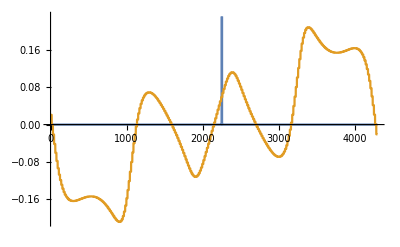

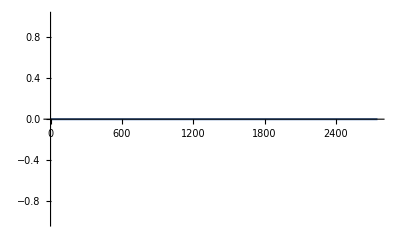

```mathematica
gateShift = 0;
(*Gate Strengths;  Multiply by zero to turn of gate*)
(*Intermediate stage is around 0.002*)
u1 = 100000*0;
u2 = 100000*1;
u3 = 100000*0;

U1 = Table[0,{i,1,Nx}];
For[i=0,i≤5,i++,
U1[[Nx-i-gateShift]]=u1
];
(*U1 = Table[0,{i,1,Nx}];
For[i=NxM/2-3,i≤NxM/2+2,i++,
U1[[Nx-i]]=u1
];*)
UM = Table[0,{i,1,NxM}];
(*For[i=NxM/2-3,i≤NxM/2+2,i++,
UM[[NxM-i]]=1000
];*)
U2=Table[0,{i,1,Nx}];
For[i=1,i≤5,i++,
U2[[i+gateShift]]=u2;
];
U3=Table[0,{i,1,Nx3}];
For[i=1,i≤40,i++,
U3[[i]]=u3
];
ListPlot[{Join[U1,UM,U2],MagΔXTop},Joined->True]
ListPlot[U3,Joined->True]
```

```mathematica
ϵ0=2 ts Cos[Pi/(Nx+1.0)];
ϵ0=2 ts Cos[1.1*Pi/(Nx+NxM+Nx3+1.0)];
Cos[1.1*Pi/(Nx+NxM+Nx3+1.0)];
Cos[Pi];
2 ts Cos[Pi/(2*Nx+NxM+1.0)]
μ=2ts Cos[Pi/(Nx+1.0)]-2ts Cos[Pi/(2*Nx+NxM+Nx3+1.0)]
```

1904.99

-0.00204568

```mathematica
ϵ0=2 ts Cos[Pi/(Nx+1.0)];
(*ϵ0=2 ts Cos[Pi/(2*Nx+NxM+Nx3+1.0)];*)
Clear[H]
H[θM_]:=Block[{Hsp},


(*First Chain*)
(*Spin up electron - chem, onsite energy, energy from y field and also gates (which is like chem). Ofd diagonal is hopping *)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
(*Spin up electron*)
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
(*Coupling betweem spin up and down, hence why it is off diagonal. Magnetic field couples them via SOC*)
H1σ12τ11=SparseArray[{Band[{1,1}]->MagX1+ⅈ MagY1,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->MagX1-ⅈ MagY1,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

(*Coupling betweem spin up and down particle and hole. This is what allows superpostion of particle hole states to make MF? This uses the superconductivty*)
H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

(*Coupling betweem spin up and down*)
H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]]; (*For all particles*)
H1τ22=-Conjugate[H1τ11];  (*Negative as for holes*)
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];


H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];

(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+UM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+UM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->MagXM+ⅈ MagYM,Band[{1,2}]->SOCMiddle*α/2,Band[{2,1}]->-SOCMiddle*α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->MagXM-ⅈ MagYM,Band[{1,2}]->-SOCMiddle*α/2,Band[{2,1}]->SOCMiddle*α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->GapMiddle*Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-GapMiddle*Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-Conjugate[HMτ11];
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];



(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->MagX2+ⅈ MagY2,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->MagX2-ⅈ MagY2,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-Conjugate[H2τ11];
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U3,Band[{1,2}]->legOnOff*ts,Band[{2,1}]->legOnOff*ts},{Nx3,Nx3}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+U3,Band[{1,2}]->legOnOff*ts,Band[{2,1}]->legOnOff*ts},{Nx3,Nx3}];
H3σ12τ11=SparseArray[{Band[{1,1}]-> MagX3+ⅈ MagY3,Band[{1,2}]->-legOnOff*ⅈ α/2,Band[{2,1}]->legOnOff*ⅈ α/2},{Nx3,Nx3}];
H3σ21τ11=SparseArray[{Band[{1,1}]->MagX3-ⅈ MagY3,Band[{1,2}]->-legOnOff*ⅈ α/2,Band[{2,1}]->legOnOff*ⅈ α/2},{Nx3,Nx3}];

H3σ12τ12=SparseArray[{Band[{1,1}]->legOnOff*ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx3,Nx3}];
H3σ21τ12=SparseArray[{Band[{1,1}]->-legOnOff*ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx3,Nx3}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-Conjugate[H3τ11];
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];(*tunneling for all different types of partciles? I.e. spin up/down particle/holes. This is within one chunk connecting all different particles from end of H11 chain to middle chain. Holes are negative hoping?*)
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx3+1}->tϕ3,{2NxM+NxM/2,2Nx3+1}->-tϕ3,{3NxM+NxM/2,3Nx3+1}->-tϕ3},{4NxM,4Nx3}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];
(*dimsize=Dimensions[Hsp];*)
Hsp
];
(*dimsize;*)
NxM;
nc=20;(*Number of values?*)
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[H[0.],-nc]]]];
```

```mathematica
m=0;
n=11+m;
nh = 10-m;
e[[n]]/Δ;
(*e[[nh]]/Δ*)
e[[n+1]]/Δ;
Clear[ψlevel];
ψlevel=Table[ (*Storing mulitple eigenstates in vector*)
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,NxM+i]]]^2+Abs[ψ[[n,2NxM+i]]]^2+Abs[ψ[[n,3NxM+i]]]^2},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i+1-4Nx-4NxM-4Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx3+i]]]^2+Abs[ψ[[n,2Nx3+i]]]^2+Abs[ψ[[n,3Nx3+i]]]^2},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx3}];
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψbar
(*StringJoin[{"ψlevel",fileInfo,"/",fileInfo,"_TopWire_Wavefunctions.eps"}]
ψlevel[n]=ψbar*)
,{n,11,12,1}];
ψleg=ψA3ue;
energyLevels = {e[[n]]/Δ,e[[n+1]]/Δ,e[[n+2]]/Δ};
Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"energyLevels","n123",".txt"}],energyLevels] ;
gateStrengths = {u1,u2,u3};
Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"gateStrengths","u123",".txt"}],gateStrengths] ;
(*e[[n+3]]/Δ*)
Dimensions[ψbar];
Dimensions[ψlevel];
Dimensions[ψlevel[[1,All]]];
ψbar;
ψlevel[[2,All]];
```

```mathematica
(*w=5*Max[Table[ψbar[[i,2]],{i,1,Length[ψbar]}]]/10; (*Scaling factor*)
TopWireWavefunctions = ListPlot[{ψbar,w MagΔXTop,w MagΔYTop},Joined->True,PlotRange->All,PlotLabel->"Top Wire Fields and Wavefunctions",AxesLabel->{"Position along x (nm)","Probabilty"},ImageSize->500,PlotLegends->{"Wavefunction","Bx Profile","By Profile"}];
(*Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_TopWire_Wavefunctions.eps"}],TopWireWavefunctions];*)
w=5*Max[Table[ψleg[[i,2]],{i,1,Length[ψleg]}]]/10;
LegWireWavefunctions = ListPlot[{ψleg,w MagΔYLeg,w MagΔXLeg},Joined->True,PlotRange->All,PlotLabel->"Leg Wire Fields and Wavefunctions",AxesLabel->{"Position along y (nm)","Probabilty"},ImageSize->500,PlotLegends->{"Wavefunction","Bx Profile","By Profile"}];*)
(*Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_LegWire_Wavefunctions.eps"}],LegWireWavefunctions];*)
```

```mathematica
ψlevelUse=ψlevel[[2,All]];
testVect=Table[ψlevelUse[[lll,2]],{lll,1,Length[ψlevelUse]}];
Dot[testVect,testVect];
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2 Nx+i]]]^2+Abs[ψ[[n,3 Nx+i]]]^2},{i,1,Nx}];
Sum[testVect[[ccc]],{ccc,1,Length[testVect]}]
```

1.

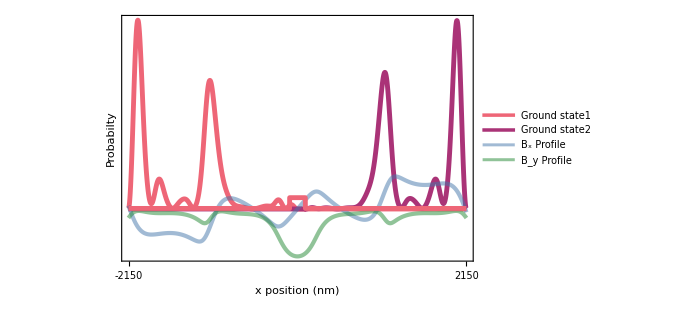

```mathematica
(*Chosing scaling factor reltiave to the eigenstate*)
ψlevel[[1,All]];
ψlevelUse=First[ψlevel];
wtop=1.2*Max[Table[ψlevelUse[[i,2]],{i,1,Length[ψlevelUse]}]];

(*This scales Bx data to fit over axes of wavefunction*)
MagXPlotTop =Table[{(i-1) totalNumPlotPointsX/(topNumPoints-1),Part[wtop MagXTop,i]},{i,1,topNumPoints}];
MagYPlotTop =Table[{(i-1) totalNumPlotPointsX/(topNumPoints-1),Part[wtop MagYTop,i]},{i,1,topNumPoints}];

wLeg=Max[Table[ψleg[[i,2]],{i,1,Length[ψleg]}]];
MagXPlotLeg =Table[{(i-1) totalNumPlotPointsY/(legNumPoints-1),Part[wLeg MagXLeg,i]},{i,1,legNumPoints}];
MagYPlotLeg =Table[{(i-1) totalNumPlotPointsY/(legNumPoints-1),Part[wLeg MagYLeg,i]},{i,1,legNumPoints}];

HeightMiddleSection =0.05*wtop;
MiddleSection=Join[Table[0.05*HeightMiddleSection,{lll,1,Nx}],Table[HeightMiddleSection,{lll,1,NxM}],Table[0.05*HeightMiddleSection,{lll,1,Nx}]];


TopWireWavefunctions = ListPlot[{ψlevel[[1,All]],ψlevel[[2,All]],MagXPlotTop,MagYPlotTop,MiddleSection},PlotStyle->{{RGBColor[238/255,102/255,119/255],Thickness[0.007]},{RGBColor[170/255,51/255,119/255],Thickness[0.007]},{RGBColor[68/255,119/255,170/255,0.5],Thickness[0.006]},{RGBColor[34/255,136/255,51/255,0.5],Thickness[0.006]}},
Joined->True,PlotRange->All,(*PlotLabel->"Top Wire Fields and Wavefunctions",*)
LabelStyle->{FontFamily->"Helvetica",18,GrayLevel[0]},ImageSize->500,

PlotLegends->Placed[LineLegend[{"Ground state1","Ground state2","B_x Profile","B_y Profile"},LabelStyle->16,LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->Directive[Green,Opacity[0]]]&),LegendMargins->5],{0.8,0.76}],

(*Frame stuff*)
Frame->True,FrameLabel->{{HoldForm["Probabilty"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{None,None},{filledTickPosXTop,emptyTickPosXTop}},
PlotRangePadding->{{0.1,0},{0.001,0.001}}]
Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_TopWire_Wavefunctions.eps"}],TopWireWavefunctions];
```

```mathematica
(*
MagAngFieldPlot=ImageResize[ResourceFunction["CombinePlots"][
postionx1=0.5;
postiony1=0.2;
ListPlot[magBTop,Joined->True,InterpolationOrder->1,PlotRange->{Automatic,{0,Max[magBTop]}},LabelStyle->{FontFamily->"Helvetica",13,GrayLevel[0]},ImageSize->{400},AspectRatio->1/4,PlotStyle->{Blue,Thickness[0.006]},FrameLabel->{{HoldForm[(*"Magnitude of Field (mT)"*)"|B| (mT)"],None},{HoldForm["x position (nm)"],None}},
Frame->True,FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{lst2,lst1}},PlotRangePadding->None

(*,PlotLegends->Placed[{"Bx Profile","By Profile"},{postionx1,postiony1}]*)],



ListPlot[(180+anglesBTop),Joined->True,InterpolationOrder->1, Frame->True,LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0],Darker[Green]},(*PlotLegends->Placed[{"By Profile"},{postionx1,postiony1}],*)PlotStyle->{Darker[Green],Thickness[0.006]},FrameLabel->(*"Angle from negative x-axis"*)"θ from negative x-axis",FrameStyle->Black,
FrameTicksStyle->{Green,Darker[Green],Red,Red},(*PlotStyle->{Blue,Directive[Green,Dashed]},*)PlotRange->{Automatic,{0,200}},FrameTicks->{{{0,30,60,90,120,150,180},Automatic},{lst2,lst1}}],

"AxesSides"->"TwoY"],{All,All}];

Overlay[{TopWireWavefunctions2,MagAngFieldPlot},Alignment->{1,-2}];
(*ImageCompose[TopWireWavefunctions,MagAngFieldPlot]*)(*end of show fucntion*)
(*GraphicsGrid[{{TopWireWavefunctions},{MagAngFieldPlot}}]*)


*)
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+runCounter.

Hold[1+runCounter]

Effetive mass m=0.04, Rahsba coupling α=0.203, Gap Δ=0.09, Gate [0, 100, 0]

1. 0.0000128644

1. 1.57355×10^-8

4.98158×10^-8 1.

1.00026 0.000230245

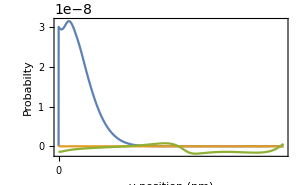
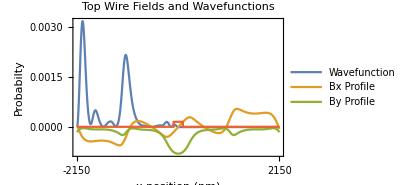
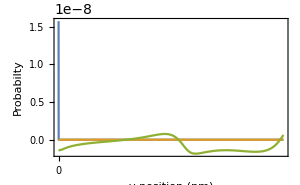
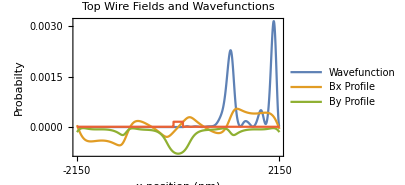
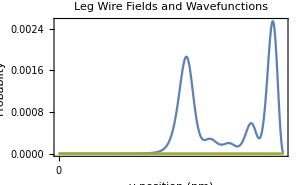
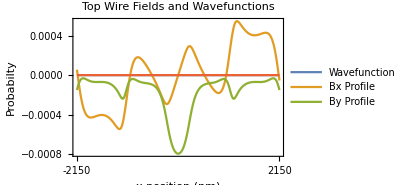
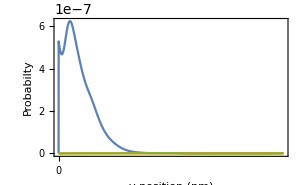
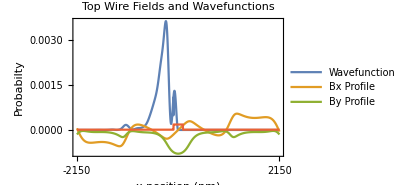
{0.00583746 Null -Graphics- -Graphics-,0.00590412 Null -Graphics- -Graphics-,0.0433289 Null -Graphics- -Graphics-,0.1114 Null -Graphics- -Graphics-}

```mathematica
(*Plotting all at same time*)
runCounter
Print["Effetive mass m=" ,ms,","," Rahsba coupling α=" ,α0,","," Gap Δ=" ,Δ,", Gate [",u1/1000,", ",u2/1000,", ",u3/1000,"]"] 
Table[
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,NxM+i]]]^2+Abs[ψ[[n,2NxM+i]]]^2+Abs[ψ[[n,3NxM+i]]]^2},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i+1-4Nx-4NxM-4Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx3+i]]]^2+Abs[ψ[[n,2Nx3+i]]]^2+Abs[ψ[[n,3Nx3+i]]]^2},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx3}];
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψleg=ψA3ue;

Clear[testVect];
testVect=Table[ψbar[[lll,2]],{lll,1,Length[ψbar]}];
testVect2=Table[ψleg[[lll,2]],{lll,1,Length[ψleg]}];


HeightMiddleSection=0.05*Max[Table[ψbar[[i,2]],{i,1,Length[ψbar]}]];
MiddleSection=Join[Table[0.05*HeightMiddleSection,{lll,1,Nx}],Table[HeightMiddleSection,{lll,1,NxM}],Table[0.05*HeightMiddleSection,{lll,1,Nx}]];

ListPlot[{ψbar,MagXPlotTop,yFieldSwitch*MagYPlotTop,MiddleSection},Joined->True,PlotRange->All,PlotLabel->"Top Wire Fields and Wavefunctions",LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]},ImageSize->300,PlotLegends->{"Wavefunction","Bx Profile","By Profile"},Frame->True,FrameLabel->{{HoldForm["Probabilty"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{filledTickPosXTop,emptyTickPosXTop}}]


(*LegWireWavefunctions =*) ListPlot[{ψleg,MagXPlotLeg,MagYPlotLeg},Joined->True,PlotRange->All,PlotLabel->"Leg Wire Fields and Wavefunctions",
LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]},ImageSize->300,(*PlotLegends->{"Wavefunction","Bx Profile","By Profile"},*)
Frame->True,FrameLabel->{{HoldForm["Probabilty"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{filledTickPosXLeg,emptyTickPosXLeg}}]
(*Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_LegWire_Wavefunctions.eps"}],LegWireWavefunctions];*)



Print[Sum[testVect[[ccc]],{ccc,1,Length[testVect]}]," ",Sum[testVect2[[ccc]],{ccc,1,Length[testVect2]}]]
e[[n]]/Δ

,{n,11,14,1}]
```

```mathematica
(*Plotting all at same time*)runCounter
Print["Effetive mass m=",ms,","," Rahsba coupling α=",α0,","," Gap Δ=",Δ,", Gate [",u1/1000,", ",u2/1000,", ",u3/1000,"]"]
Table[ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2 Nx+i]]]^2+Abs[ψ[[n,3 Nx+i]]]^2},{i,1,Nx}];
ψAMue=Table[{i-1-3 Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,NxM+i]]]^2+Abs[ψ[[n,2 NxM+i]]]^2+Abs[ψ[[n,3 NxM+i]]]^2},{i,4 Nx,4 Nx+NxM}];
ψA2ue=Table[{i-1-3 Nx-3 NxM,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2 Nx+i]]]^2+Abs[ψ[[n,3 Nx+i]]]^2},{i,4 Nx+4 NxM,4 Nx+4 NxM+Nx}];
ψA3ue=Table[{i+1-4 Nx-4 NxM-4 Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx3+i]]]^2+Abs[ψ[[n,2 Nx3+i]]]^2+Abs[ψ[[n,3 Nx3+i]]]^2},{i,4 Nx+4 NxM+4 Nx,4 Nx+4 NxM+4 Nx+Nx3}];
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψleg=ψA3ue;
Clear[testVect];
testVect=Table[ψbar[[lll,2]],{lll,1,Length[ψbar]}];
testVect2=Table[ψleg[[lll,2]],{lll,1,Length[ψleg]}];
HeightMiddleSection=0.05*Max[Table[ψbar[[i,2]],{i,1,Length[ψbar]}]];
MiddleSection=Join[Table[0.05*HeightMiddleSection,{lll,1,Nx}],Table[HeightMiddleSection,{lll,1,NxM}],Table[0.05*HeightMiddleSection,{lll,1,Nx}]];
ListPlot[{ψbar,MagXPlotTop,yFieldSwitch*MagYPlotTop,MiddleSection},Joined->True,PlotRange->All,PlotLabel->"Top Wire Fields and Wavefunctions",LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]},ImageSize->300,PlotLegends->{"Wavefunction","Bx Profile","By Profile"},Frame->True,FrameLabel->{{HoldForm["Probabilty"],None},{HoldForm["x position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{filledTickPosXTop,emptyTickPosXTop}}]
(*LegWireWavefunctions=*) ListPlot[{ψleg,MagXPlotLeg,MagYPlotLeg},Joined->True,PlotRange->All,PlotLabel->"Leg Wire Fields and Wavefunctions",LabelStyle->{FontFamily->"Helvetica",14,GrayLevel[0]},ImageSize->300,(*PlotLegends->{"Wavefunction","Bx Profile","By Profile"},*)Frame->True,FrameLabel->{{HoldForm["Probabilty"],None},{HoldForm["y position (nm)"],None}},FrameStyle->Directive[Black,Thickness[Small]],FrameTicks->{{Automatic,Automatic},{filledTickPosXLeg,emptyTickPosXLeg}}]
(*Export[StringJoin[{"Mathematica_out/",fileInfo,"/",fileInfo,"_LegWire_Wavefunctions.eps"}],LegWireWavefunctions];*) Print[Sum[testVect[[ccc]],{ccc,1,Length[testVect]}]," ",Sum[testVect2[[ccc]],{ccc,1,Length[testVect2]}]] e[[n]]/Δ,{n,11,14,1}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+runCounter.

Hold[1+runCounter]

Effetive mass m=0.04, Rahsba coupling α=0.203, Gap Δ=0.09, Gate [0, 100, 0]

1. 0.0000128644

1. 1.57355×10^-8

4.98158×10^-8 1.

1.00026 0.000230245

{0.00583746 Null -Graphics- -Graphics-,0.00590412 Null -Graphics- -Graphics-,0.0433289 Null -Graphics- -Graphics-,0.1114 Null -Graphics- -Graphics-}